# 超椭圆

### 超椭圆 （superellipse） 也称为拉梅曲线 （Lamé curve），是在笛卡儿坐标系下满足以下方程式的点的集合：其中n、a及b为正数。

```mathematica
Manipulate[
ContourPlot[Abs[x]^n+Abs[y]^n==1,{x,-1,1},{y,-1,1}],
{n,1/2,10,1/2}]
```

```mathematica
f[x_,n_]:=Sign[x] Abs[x]^n;
Manipulate[ParametricPlot[{f[Cos[θ],n],f[Sin[θ],n]},{θ,0,2π}],{n,0.5,15,0.5}]
```

## 方圆形

### n = 4，且a = b的超椭圆，看起来像是 "正方形的轮子"。

## 三尖瓣线

### 三尖瓣线可以用以下的参数方程表示：

### 其中a是小圆的半径，b是大圆 （也就是小圆在其内侧无滑动滚动） 的半径 （此处b = 3 a）。

## 星形线

### 当n=2/3时，得到星形线，如下使用参数方程绘制

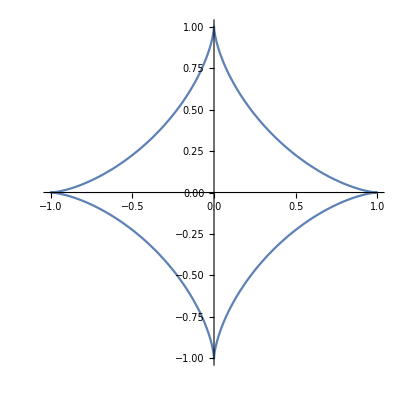

```mathematica
ParametricPlot[{Cos[θ]^3,Sin[θ]^3},{θ,0,2π}]
```

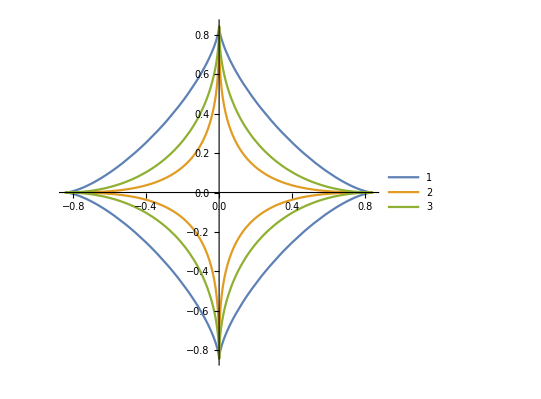

```mathematica
ParametricPlot[{{Cos[t]^2 Sin[Cos[t]],Sin[t]^2 Sin[Sin[t]]},{Cos[t]^4 Sin[Cos[t]],Sin[t]^4 Sin[Sin[t]]},{Abs[Cos[t]]^3 Sin[Cos[t]],Abs[Sin[t]]^3 Sin[Sin[t]]}},{t,0,2π},PlotLegends->Automatic]
```

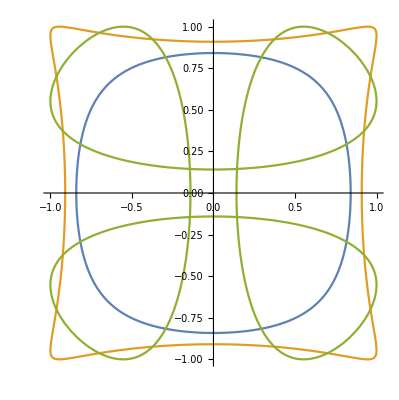

```mathematica
ParametricPlot[{{Sin[Cos[t]],Sin[Sin[t]]},{Sin[2Cos[t]],Sin[2Sin[t]]},{Sin[3Cos[t]],Sin[3Sin[t]]}},{t,0,2π}]
```

```mathematica
Manipulate[ParametricPlot[{Sin[ a Cos[t]],Sin[a Sin[t]]},{t,0,2π}],
{a,1,20}]
```

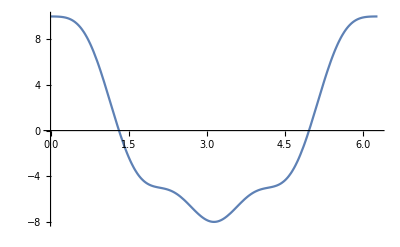

```mathematica
Plot[{9Cos[θ]+2Cos[2θ]-Cos[4θ]},{θ,0,2Pi}]
```

```mathematica
ParametricPlot3D[
{Abs[Cos[t]]^0.5 Sign[Cos[t]](9Sin[θ]-2Sin[2θ]-Sin[4θ]),
Abs[Sin[t]]^0.5 Sign[Sin[t]],
(9Sin[θ]-2Sin[2θ]-Sin[4θ])},{t,0,2π},{θ,0,2π}]
```

-Graphics3D-